```mathematica
Func20[x_]:=Module[{R1,R2},
R1 = Sin[(√13 x^3-9x-5-√17)/10];
R2 = Tan[(x^2+x+2^(1/3))/(3x-5)];
Return [R1 + R2 + 0.6]
];
Func23[x_]:=Module[{R1,R2},
R1 = Sin[(-2 x^2-√10 x+1)/4];
R2 = ((x^2+(√2+R1)*x - 3)/(R1*x - 3))^Log[2];
Return [R1 + R2 -1.2]
];
pointsgrid[a_,b_,i_,n_]:=a + (i-1) * (b-a)/(n-1);
ii[x_]:=x;
xx[x_]:=x^2;
Si[x_]:=Sin[π*x];
```

```mathematica
SetDirectory[NotebookDirectory[]];
f =xx;
var = "20";
namex=StringJoin["output/vecx",var,".dat"];
namey = StringJoin["output/vecy",var,".dat"];
nameintery= StringJoin["output/vecintery",var,".dat"];
x =Flatten@ Import[namex];
y =Flatten@  Import[namey];
intery =Flatten@  Import[nameintery];
points=Table[{x⟦i⟧,y⟦i⟧},{i,1,Length@x}];
interpoints = Table[{pointsgrid[x⟦1⟧,x⟦-1⟧,i,Length@intery],intery⟦i⟧},{i,1,Length@intery}];
```

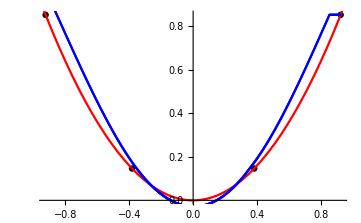

```mathematica
Discret= ListPlot[points,PlotRange->All,PlotStyle->{Black}];
Reall = Plot[f[x],{x,-1,1},PlotStyle->{Red},PlotRange->All];
Inter=ListPlot[interpoints,PlotRange->All,PlotStyle->{Blue}];
Show[Discret,Reall,Inter]
```

```mathematica
x = {-1,-0.7778,-0.5556,-0.3333,-0.1111, 0.1111, 0.3333, 0.5556, 0.7778, 1};
```

```mathematica
y = {0.07691, 0.07793,-0.009699,-0.1603,-0.3474,-0.5532,-0.7856,-1.116,-1.919, 16.49};
```

```mathematica
h[i_]:= x[[i]] - x[[i - 1]];
```

```mathematica
a[i_]:= h[i];
```

```mathematica
b[i_] := 2 * (h[i] + h[i + 1]);
```

```mathematica
c[i_] := h[i + 1];
```

```mathematica
d[i_] := 6 *( (y[[i+1]] - y[[i]])/h[i + 1] - (y[[i]] - y[[i - 1]])/h[i])
```

```mathematica
matrx = ({{b[2], c[2], 0, 0, 0, 0, 0, 0}, {a[3], b[3], c[3], 0, 0, 0, 0, 0}, {0, a[4], b[4], c[4], 0, 0, 0, 0}, {0, 0, a[5], b[5], c[5], 0, 0, 0}, {0, 0, 0, a[6], b[6], c[6], 0, 0}, {0, 0, 0, 0, a[7], b[7], c[7], 0}, {0, 0, 0, 0, 0, a[8], b[8], c[8]}, {0, 0, 0, 0, 0, 0, a[9], b[9]}})
```

{{0.8888,0.2222,0,0,0,0,0,0},{0.2222,0.889,0.2223,0,0,0,0,0},{0,0.2223,0.889,0.2222,0,0,0,0},{0,0,0.2222,0.8888,0.2222,0,0,0},{0,0,0,0.2222,0.8888,0.2222,0,0},{0,0,0,0,0.2222,0.889,0.2223,0},{0,0,0,0,0,0.2223,0.889,0.2222},{0,0,0,0,0,0,0.2222,0.8888}}

```mathematica
matrx // MatrixForm
```

(0.8888 | 0.2222 | 0 | 0 | 0 | 0 | 0 | 0
0.2222 | 0.889 | 0.2223 | 0 | 0 | 0 | 0 | 0
0 | 0.2223 | 0.889 | 0.2222 | 0 | 0 | 0 | 0
0 | 0 | 0.2222 | 0.8888 | 0.2222 | 0 | 0 | 0
0 | 0 | 0 | 0.2222 | 0.8888 | 0.2222 | 0 | 0
0 | 0 | 0 | 0 | 0.2222 | 0.889 | 0.2223 | 0
0 | 0 | 0 | 0 | 0 | 0.2223 | 0.889 | 0.2222
0 | 0 | 0 | 0 | 0 | 0 | 0.2222 | 0.8888)

```mathematica
values // MatrixForm
```

(-2.39376
-1.69858
-0.987401
-0.50495
-0.718272
-2.64225
-12.7655
518.776)

```mathematica
values = ({{d[2]}, {d[3]}, {d[4]}, {d[5]}, {d[6]}, {d[7]}, {d[8]}, {d[9]}}) // Flatten
```

{-2.39376,-1.69858,-0.987401,-0.50495,-0.718272,-2.64225,-12.7655,518.776}

```mathematica
LinearSolve[matrx, values] // MatrixForm
```

(-2.47494
-0.873241
-1.67495
3.13119
-13.1223
46.1255
-183.23
629.489)